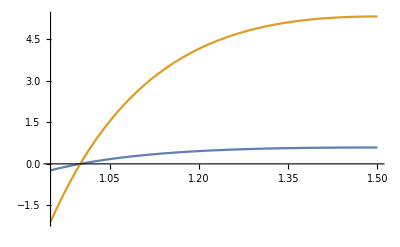

```mathematica
Vf[r_,rs_,L_]=(1-rs/r)L^2/r^2;
Plot[{Vf[r,1,2],Vf[r,1,6]},{r,0.95,1.5}]
```

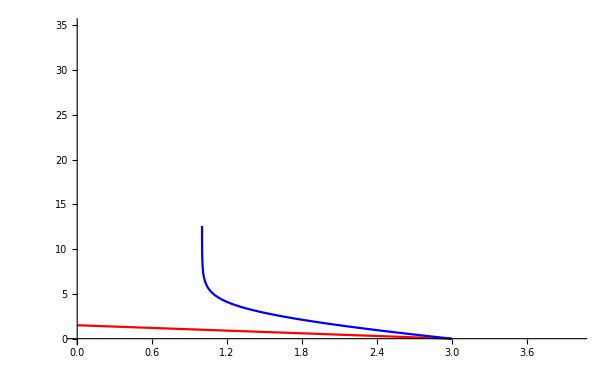

```mathematica
τ[r_,ro_,Ε_]=(ro-r)/Ε;
t[r_,ro_,rs_]=ro-r+rs*Log[(ro-rs)/(r-rs)];
Plot[{τ[r,3,2],t[r,3,1]},{r,0,4},PlotStyle->{Red,Blue},PlotRange->{0,35}]
```

```mathematica
p3[x_]=a3 x^3+a2 x^2+a1 x+a0;
p3[z-a2/(3 a3)]//Expand
```

a0+(2 a2^3)/(27 a3^2)-(a1 a2)/(3 a3)+a1 z-(a2^2 z)/(3 a3)+a3 z^3

```mathematica
Collect[%,z]
```

a0+(2 a2^3)/(27 a3^2)-(a1 a2)/(3 a3)+(a1-a2^2/(3 a3)) z+a3 z^3

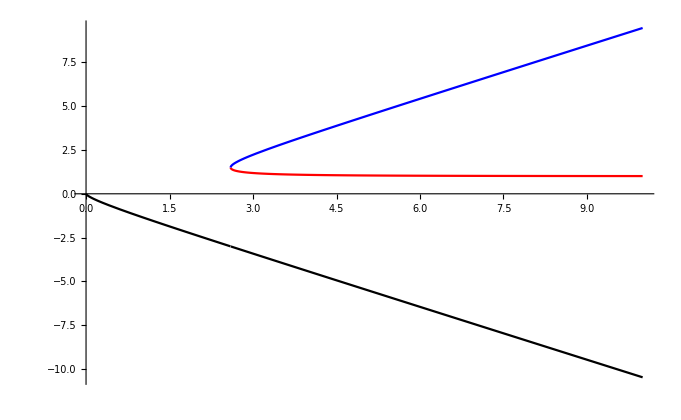

```mathematica
bc=(3 √3)/2 rs;
θ=1/3 ArcSin[bc/b];
R[b_,rs_,n_]=(2 √3)/3 b Sin[θ+(2 n π)/3];
Plot[{R[b,1,0],R[b,1,1],R[b,1,2]},{b,0,10},PlotStyle->{Red,Blue,Black}]
```

```mathematica
ro[b_,rs_]=R[b,rs,0]
```

(2 b Sin[1/3 ArcSin[(3 √3 rs)/(2 b)]])/(√3)

```mathematica
r1[b_,rs_]=TrigExpand[R[b,rs,1]]
```

b Cos[1/3 ArcSin[(3 √3 rs)/(2 b)]]-(b Sin[1/3 ArcSin[(3 √3 rs)/(2 b)]])/(√3)

```mathematica
r2[b_,rs_]=TrigExpand[R[b,rs,2]]
```

-b Cos[1/3 ArcSin[(3 √3 rs)/(2 b)]]-(b Sin[1/3 ArcSin[(3 √3 rs)/(2 b)]])/(√3)

```mathematica
ro[bc,rs]
```

(3 rs)/2

```mathematica
r1[bc,rs]
```

(3 rs)/2

```mathematica
r2[bc,rs]
```

-3 rs

```mathematica
Limit[ro[b,rs],b->∞]
```

rs

```mathematica
TrigExpand[Sin[a+4/3 π]]
```

-1/2 √3 Cos[a]-Sin[a]/2

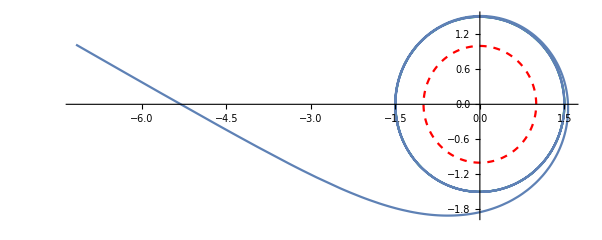

```mathematica
ϕ0=2ArcTanh[1/(√3)];
r[ϕ_,rs_]=(3 rs)/(3 Tanh[1/2(ϕ-ϕ0)]^2-1);
g1=PolarPlot[{1,1.5},{ϕ,0,2π},PlotStyle->{{Dashed,Red},{Dashed,Green}}];
g2=PolarPlot[{r[ϕ,1]},{ϕ,3,25}];
Show[g1,g2]
```

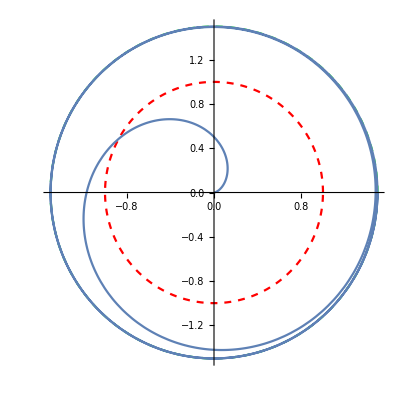

```mathematica
rseg[ϕ_,rs_]=(3 rs)/2((1-Exp[ϕ])^2/(1+4Exp[ϕ]+Exp[2ϕ]));
g3=PolarPlot[{rseg[ϕ,1]},{ϕ,0,6π}];
Show[g1,g3]
```

```mathematica
D[Tan[x/2]^2, x]
```

Sec[x/2]^2 Tan[x/2]

```mathematica
∫1/Sin[x/2] ⅆx
```

-2 Log[Cos[x/4]]+2 Log[Sin[x/4]]

```mathematica
a[V_,T1_,T2_,P1_,P2_]=V^2((P2 T1-P1 T2)/(T2-T1));
b[V_,Rc_,T1_,T2_,P1_,P2_]=(((P2 -P1)V -Rc(T2-T1))/(P2-P1));
```

```mathematica
a[0.25,300,350,90,110]
```

1.875

```mathematica
b[0.25,0.082,300,350,90,110]
```

0.045

```mathematica
Solve[1-rs/x-x/rγ==0,x]
```

{{x→1/2 (rγ-√(-4 rs rγ+rγ^2))},{x→1/2 (rγ+√(-4 rs rγ+rγ^2))}}

```mathematica
JacobiSN
```

## Null FK

p = r1

```mathematica
Q=√((r1[b,rs]-rs)(r1[b,rs]+3rs));
k=√((Q-r1[b,rs]+3rs)/(2Q));
ϕ0=EllipticK[k^2];
β0=1/2 √(Q/r1[b,rs]);
Cn[x_,y_]=JacobiCN[x,y];
α=(Q-r1[b,rs]+3rs)/(2rs);
```

```mathematica
r[ϕ_,b_,rs_]=r1[b,rs]/(1-α Cn[ϕ0-β0*ϕ,k^2]^2);
```

```mathematica
bi[rs_]=8/9 √3 bc
```

4 rs

```mathematica
rp[ϕ_,rs_]=r[ϕ,bi[rs],rs];
rp2[ϕ_,rs_]=r[ϕ,1.5*bi[rs],rs];
```

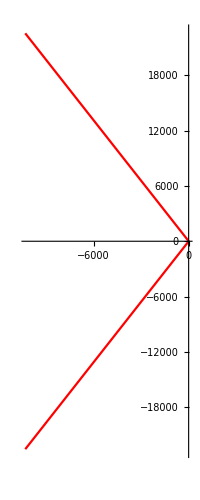

```mathematica
g1=PolarPlot[{1,3},{ϕ,0,2π},PlotStyle->{{Dashed,Black},{Dashed,Black}}];
g2=PolarPlot[{rp[ϕ,1]},{ϕ,-2,2},PlotStyle->{Red}];
g3=PolarPlot[{rp2[ϕ,1]},{ϕ,-1,1},PlotStyle->{Green}];
Show[g1,g2,g3]
```

```mathematica
Manipulate[PolarPlot[rp[ϕ,rs],{ϕ,-2,2}],{rs,3,8}]
```

## Null SK

```mathematica
Nc[x_,y_]=JacobiNC[x,y];
Rs[ϕ_,b_,rs_]=r1[b,rs]/(1+α Nc[β0*ϕ,k^2]^2);
```

```mathematica
Rp[ϕ_,rs_]=Rs[ϕ,bi[rs],rs];
Rp2[ϕ_,rs_]=Rs[ϕ,1.5*bi[rs],rs];
```

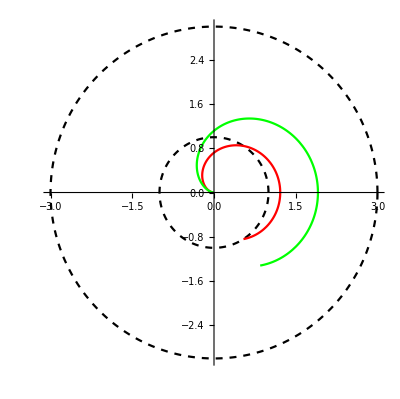

```mathematica
G2=PolarPlot[{Rp[ϕ,1]},{ϕ,-1,π},PlotStyle->{Red}];
G3=PolarPlot[{Rp2[ϕ,1]},{ϕ,-1,π},PlotStyle->{Green}];
Show[g1,G2,G3]
```

## TIME - LIKE GEODESICS

```mathematica
V[r_,rs_,L_]=(1-rs/r)(1+L^2/r^2);
Vp[r_,rs_,L_]=D[V[r,rs,L], r]//Simplify
```

(r^2 rs+L^2 (-2 r+3 rs))/r^4

```mathematica
rc1=r/.Solve[r^2 rs+L^2 (-2 r+3 rs)==0,r][[1]]
rc2=r/.Solve[r^2 rs+L^2 (-2 r+3 rs)==0,r][[2]]
```

(L^2-√(L^4-3 L^2 rs^2))/rs

(L^2+√(L^4-3 L^2 rs^2))/rs

```mathematica
Vc1=V[rc1,rs,L]//Expand
```

1-(L^2 rs^4)/((L^2-√(L^4-3 L^2 rs^2))^3)+(L^2 rs^2)/((L^2-√(L^4-3 L^2 rs^2))^2)-rs^2/(L^2-√(L^4-3 L^2 rs^2))

```mathematica
Vc2=V[rc2,rs,L]//Expand
```

1-(L^2 rs^4)/((L^2+√(L^4-3 L^2 rs^2))^3)+(L^2 rs^2)/((L^2+√(L^4-3 L^2 rs^2))^2)-rs^2/(L^2+√(L^4-3 L^2 rs^2))

```mathematica
Manipulate[Plot[{1,V[r,rs,√3 rs],V[r,rs,1.8rs],V[r,rs,2rs]},{r,0,25},PlotRange->{0.8,1.05},PlotStyle->{Dashed,Black,Red,Blue}],{rs,1,5}]
```

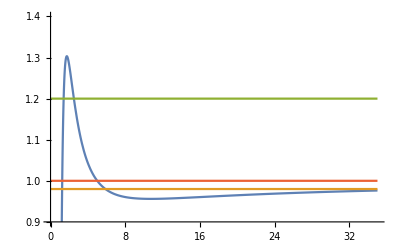

```mathematica
Plot[{V[r,1,2.5],0.98,1.2,1},{r,0,35},PlotRange->{0.9,1.4}]
```